```mathematica
Needs["NDSolve`FEM`"]

(*Konstanten*)
c = 343;
f = 40000;
ρ = 1.225;

(*resultierend*)
ω = N[2 Pi f];
λ =N[ c/f];
T =N[1/f] ;

Monitor[
result = Table[

(*Problem definition*)
reg=Disk[{0,0},0.1,{0,π}]; (*region*)
bc=NeumannValue[-(I ω)/(ρ c)*p[x,y],y>0]; (*boundary Condition*)

Module[{n=1,depth= iterator*λ,distance =1/2 λ,holeDia,transDia = 0.01,transDist},
holeDia =1/4 λ;
transDist=distance-holeDia+transDia;
Do[
reg = RegionUnion[reg,
Polygon[{
{i*distance-holeDia/2,0},{i*distance+holeDia/2,0},
{i*transDist+transDia/2,-depth},{i*transDist-transDia/2,-depth}
}] 
];
bc+=NeumannValue[-(I ω)/(ρ c)*(p[x,y]+2),y==-depth&& i*transDist-transDia/2<x<i*transDist+transDia/2];
,{i,-(n-1)/2,(n-1)/2}];
];

(*RegionPlot[reg,AspectRatio->Automatic,]*)

(*Mesh generation*)
mesh=ToElementMesh[reg,
MaxCellMeasure->λ^2/50,
"MaxBoundaryCellMeasure"->λ/8,
"BoundaryMeshGenerator"->{"BoundaryDiscretizeRegion","SamplePoints"->200},
MeshQualityGoal->"Maximal",
MeshRefinementFunction-> Function[{vertices,area},
(Mean[vertices][[2]]<0.01 && area>λ^2/100)
],
"MeshOrder"->2
];
(*MeshRegion[mesh,,PlotTheme->"Lines"]*)

(*Solve Model*)
pde={-(ω^2 p[x,y])/(c^2 ρ)+Div[({{-1/ρ, 0}, {0, -1/ρ}}).Grad[p[x,y],{x,y}],{x,y}]==bc};
pfun=NDSolveValue[pde,p,{x,y}∈mesh];

{iterator * λ, pfun},

{iterator, 3,6,0.1}],ProgressIndicator[iterator,{3,6}]];//Timing
(*save the result*)
ByteCount[result]
SetDirectory[NotebookDirectory[]];
Save["Optimisierung_Kanal_Laenge.m",result]
```

{156.061,Null}

75864784

```mathematica
(*get Data from file*)
SetDirectory[NotebookDirectory[]];
Get["Optimisierung_Kanal_Laenge.m"]
```

```mathematica
result[[1,2]][0,0]
```

-1.63158-0.610797 ⅈ

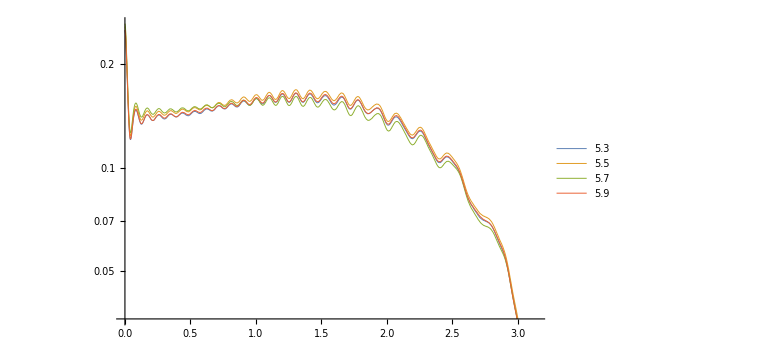

```mathematica
funct = Table[
{Norm[result[[i,2]][0.1Cos[θ],0.1Sin[θ]]],
result[[i,1]]/λ}
,
{i,24,30,2}];
LogPlot[
Evaluate[funct[[All,1]]],
{θ,0,Pi},
PlotStyle->AbsoluteThickness[0.7],
ImageSize->Large,
PlotLegends->Placed[funct[[All,2]],Automatic]
]
```